# Numerical Solutions to Volterra Equations of the First Kind

Version 1.30
copyright © 2002-Year Michael Honeychurch

Reference: Nicholson, R.S.and M.L.Olmstead, (1972). Numerical solution of integral equations. In Electrochemistry; Calculations, Simulations, and Instrumentation, (eds. J.S. Mattson, H.B. Mark jnr., H.C. MacDonald jnr.), pp.119-138, Marcel Dekker, New York.

## Mathematica Preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"],Clear["Global`*"]];
```

```mathematica
SetOptions[ListPlot,
Axes->False,
Background->Automatic,
FormatType->TraditionalForm,
FrameLabel->None,
Frame->True,
FrameStyle->{ColorData["Legacy","NavyBlue"],AbsoluteThickness[.7]},FrameTicks->Automatic,
GridLines->None,
ImageSize->288,
Joined->True,
PlotLabel->None];
```

```mathematica
cvTicks1[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],2.5}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-2.5}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.5}]];

cvTicks2[min_,max_]:=Join[Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],.1}],Table[{x,x,{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-.1}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.02}]];

cvTicks3[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],2.5}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-2.5}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.5}]];

cvTicks4[min_,max_]:=Join[Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Ceiling[max],.1}],Table[{x,"",{0.02,0},{RGBColor[0,0,1]}},{x,0,Floor[min],-.1}],Table[{x,"",{0.01,0},{RGBColor[0,0,1]}},{x,Floor[min],Ceiling[max],0.02}]];
```

```mathematica
optionC={
PlotRange-> {{-10,10}, {0, -0.5}},
AxesOrigin-> {-10,0},
PlotStyle-> {Blue,AbsoluteThickness[0.7]},
FrameTicks-> {cvTicks1,cvTicks2,cvTicks3,cvTicks4},
FrameLabel->{
Style["\!\(nF\/RT\)(E-E°)",FontFamily-> "Times New Roman",FontColor-> Black,FontSlant-> Italic,FontSize-> 12],Style["χ",FontFamily-> "Times New Roman",FontSlant-> Italic,FontColor->Black,FontSize-> 12],
None,
None}};
```

```mathematica
Clear[LowerDiagonalMatrix];

LowerDiagonalMatrix[f_,n_Integer?NonNegative]:=Array[If[#>=#2,f[##],0]&,{n,n}]
```

```mathematica
$Line=0;
```

## Huber's Method

### General solution

```mathematica
Clear[d,n,g,b,f,m,h];

h[k_]:=4/3*d^(3/2)*(k^(3/2)-(k-1)^(3/2))
d=0.05;
n=400;
g:=1/(1+(Exp[10]*Exp[-m*d]));
b=ConstantArray[0.,{n}];
f=ConstantArray[0.,{n}];
```

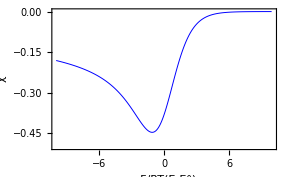

```mathematica
For[m=1,m<n+1,m++,b⟦m⟧=g/h[1]-1/h[1]*∑_(i=1)^(m-1) b⟦i⟧*h[m-i+1]];
f⟦1⟧=(d*b⟦1⟧);

For[m=2,m<n+1,m++,f⟦m⟧=(d*b⟦m⟧)+f⟦m-1⟧]

result=Table[{10-(m*d),-Sqrt[Pi]*f⟦m⟧},{m,1,n}];

ListPlot[result,optionC]
```

### Procedural Implementation of Huber's Method

```mathematica
Clear[d,n,g,b,f,m];

d=0.2;
n=100;
g:=0.75/((1+Exp[10.-m*d])*d^(3/2))
a=ConstantArray[0.,{n}];
f=ConstantArray[0.,{n}];
```

```mathematica
For[m=1,m<n+1,m++,a⟦m⟧=g-∑_(i=1)^(m-1) a⟦i⟧*((m-i+1)^(3/2)-(m-i)^(3/2))];
f⟦1⟧=(d*a⟦1⟧);
For[m=2,m<n+1,m++,f⟦m⟧=(d*a⟦m⟧)+f⟦m-1⟧]
result=Table[{10-(m*d),-Sqrt[Pi]*f⟦m⟧},{m,1,n}];
```

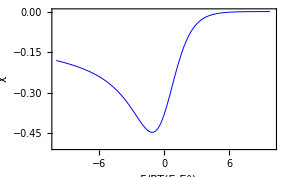

```mathematica
ListPlot[result,optionC]
```

### Functional Implementation of Huber's Method

```mathematica
Clear[d,n,g,d,x,mat,a,f,result];

d=0.1;
n=200;
g=Table[0.75/((1+Exp[10-i*d])*d^(3/2)),{i,n}];
v=Table[((n-i+1)^(3/2)-(n-i)^(3/2))//N,{i,n,1,-1}];
x[r_,s_]:=v⟦r-s+1⟧;

mat=LowerDiagonalMatrix[x,n];
a=LinearSolve[mat,g];
f=Table[0.,{n}];
f⟦1⟧=(d*a⟦1⟧);

result=Map[{10-(#*d),-Sqrt[Pi]*Set[f⟦#⟧,(d*a⟦#⟧)+f⟦#-1⟧]}&,Range[2,n]];
```

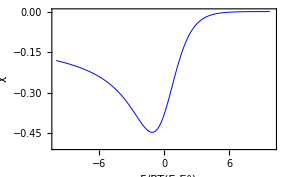

```mathematica
ListPlot[result,optionC]
```